```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/thermodynamic_integration_analysis/GibbsBog/4_LONG50000_4.8_2_3_v1v2"];
dudlFiles={"T_all_vol_dUdL"};
(*Data format, col1=L, col2=vol1, col2=vol2...*)
dudlDat=Table[ReadList[dudlFiles[[i]],{Number, Number,Number,Number,Number,Number}],{i,1,1}];
dudlV1=Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[2]]}],11];
dudlAll=Table[Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[1+vol]]}],11],{vol,1,5}];
```

```mathematica
dudlAllFit1=Table[Table[Fit[dudlAll[[vol]][[temp]],{1L,1},L],{temp,1,6,1}],{vol,1,5}];
dudlAllFit2=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^2,L,1},L],{temp,1,6,1}],{vol,1,5}];
dudlAllFit3=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,5}];
dudlAllFit4=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^4,L^2,L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,5}];
```

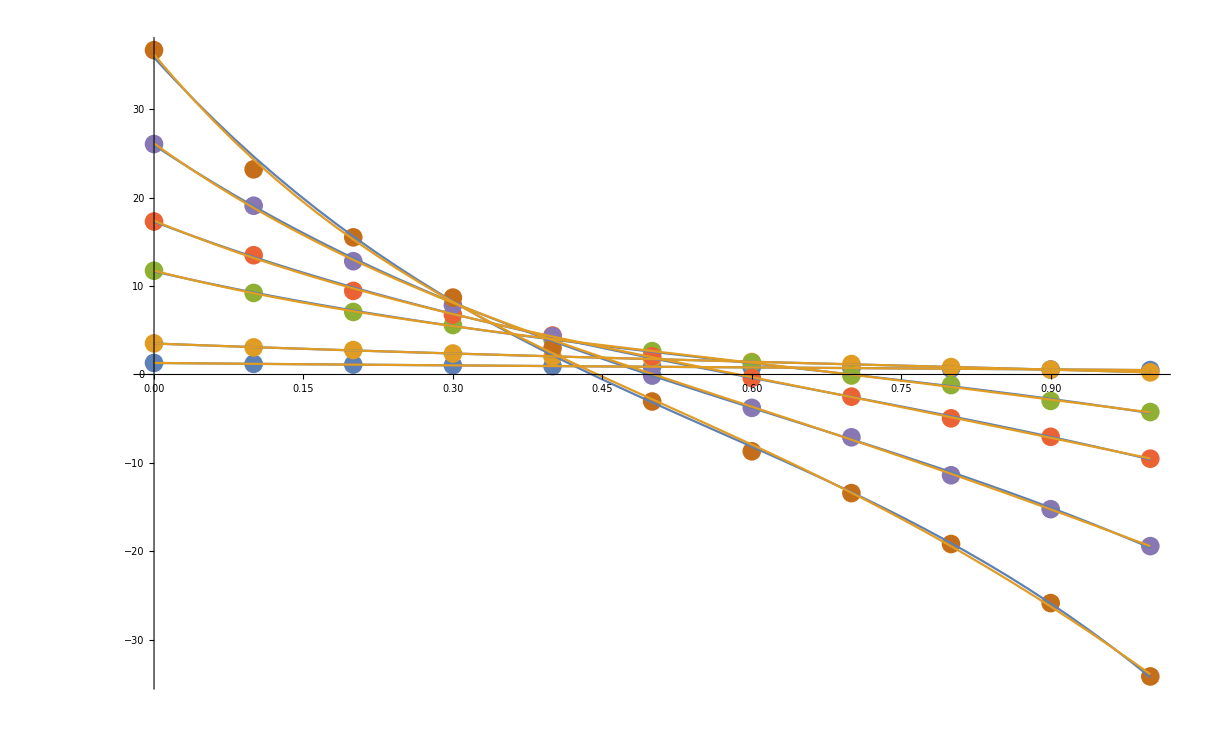

```mathematica
Show[ListPlot[dudlAll[[1]]],Plot[{dudlAllFit3[[1]],dudlAllFit4[[1]]},{L,0,1}]]
```

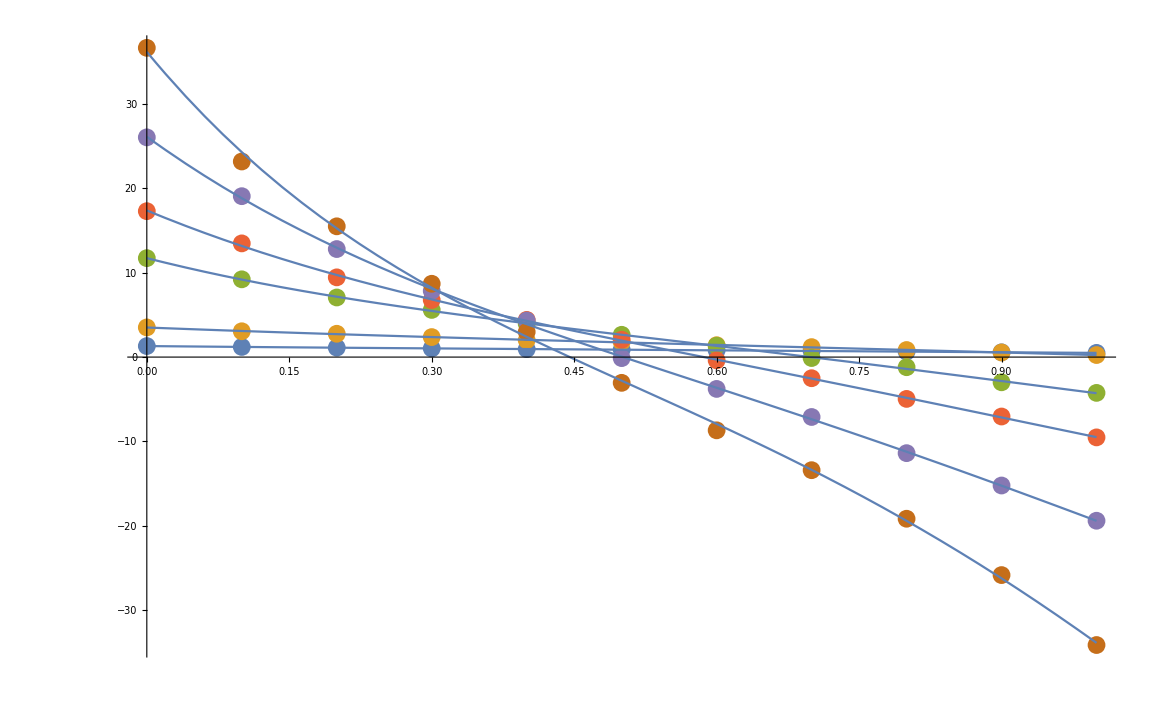

```mathematica
Show[ListPlot[dudlAll[[1]]],Plot[dudlAllFitD4[[1]],{L,0,1}]]
```

```mathematica
bound1=0;bound2=1; 

(*Solver 1 - standard *)
mvtSolver[function_]:=Solve[Evaluate@function==(Integrate[Evaluate@function,{L,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2})&&L∈Interval[{0,1}],L,Reals]//N
mvtSolverNum[arg_]:=mvtSolver[arg][[1]][[1]][[2]][[1]]
(*Integrator*)
dudlIntegrator[function_]:=NIntegrate[function,{L,bound1,bound2}]
(*Solver 2 - midpoint*)
midValintValMVT[fun_]:={mvtSolver[fun],
fun/.L->0.5,
dudlIntegrator[fun]}
(*Solver 3 - l1 l2 norm CS inpsired solver *)
weightedMVT[fun_,mu_,nu_,midpoint_]:=nu*NMinimize[(Evaluate[fun/.{L->mvtSolverNum[fun]}]-fun/.L->x)^2+mu*(midpoint-x)^2,x]
mvtNumWeight[arg_,mu_,nu_,midpoint_]:={mvtSolver[arg][[1]][[1]][[2]][[1]],weightedMVT[arg,mu,nu,midpoint]}
```

```mathematica
(*Goal - obtain a MVT value of L, subject to constraint that the Fah value should be as close to the L=0.5 Fah as possible*)
```

```mathematica
weightedMVT[dudlAllFit4[[1]][[1]],0.01,0.5]
weightedMVT[dudlAllFit4[[1]][[2]],0.01,0.5]
mvtNumWeight[dudlAllFit4[[1]][[2]],0.01,0.5]
```

{6.53416×10^-7,{x→0.491986}}

{1.82196×10^-6,{x→0.486509}}

{0.486495,{1.82196×10^-6,{x→0.486509}}}

```mathematica
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],0.01,1,0.5],{i,1,6}]//TableForm
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],1000,1,0.5],{i,1,6}]//TableForm
```

0.491846 | 6.53416×10^-7
x→0.491986
0.486495 | 1.82196×10^-6
x→0.486509
0.480064 | 3.97421×10^-6
x→0.480065
0.476541 | 5.5032×10^-6
x→0.476541
0.476548 | 5.49986×10^-6
x→0.476548
0.482072 | 3.21399×10^-6
x→0.482072

0.491846 | 0.000037955
x→0.499995
0.486495 | 0.00166196
x→0.499877
0.480064 | 0.0598788
x→0.497002
0.476541 | 0.189855
x→0.491924
0.476548 | 0.322485
x→0.486261
0.482072 | 0.23225
x→0.487048

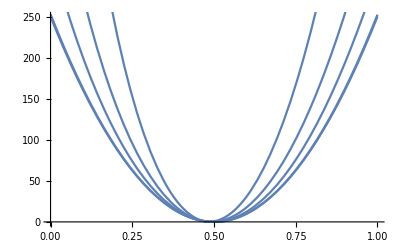

```mathematica
Show@Table[With[{fun=dudlAllFit4[[1]][[i]],mu=1000,nu=1,midpoint=0.5},Plot[(Evaluate[fun/.{L->mvtSolverNum[fun]}]-fun/.L->x)^2+mu*(midpoint-x)^2,{x,0,1}]],{i,1,5}]
```

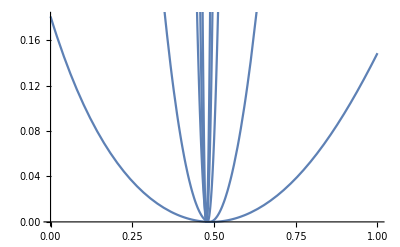

```mathematica
Show@Table[With[{fun=dudlAllFit4[[1]][[i]],mu=0,nu=1,midpoint=0.5},Plot[(Evaluate[fun/.{L->mvtSolverNum[fun]}]-fun/.L->x)^2+mu*(midpoint-x)^2,{x,0,1}]],{i,1,5}]
```

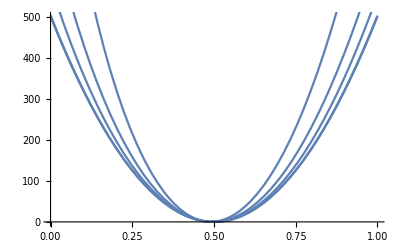

```mathematica
Show@Table[With[{fun=dudlAllFit4[[1]][[i]],mu=2000,nu=1,midpoint=0.5},Plot[(Evaluate[fun/.{L->mvtSolverNum[fun]}]-fun/.L->x)^2+mu*(midpoint-x)^2,{x,0,1}]],{i,1,5}]
```

```mathematica
ttt={300,760,1900,2500,3200,3805};
```

```mathematica
Table[Table[dudlAllFit4[[j]][[i]]/.L->{dataMVT[[i]],dataWMVT[[i]]},{i,1,5}],{j,1,5}];
```

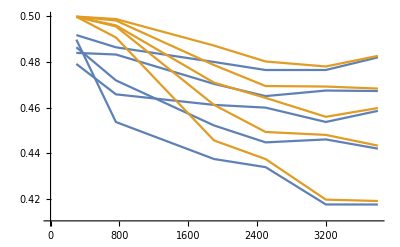

```mathematica
dataMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],100,1,0.5][[1]]},{i,1,6}],{j,1,5}];
dataWMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],100,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,5}];
Show[Table[ListLinePlot[{dataMVT4[[i]],dataWMVT4[[i]]},PlotRange->{{0,3800},{0.41,0.5}}],{i,1,5}]]
```

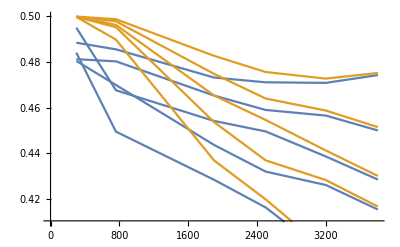

```mathematica
dataMVT3=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit3[[j]][[i]],100,1,0.5][[1]]},{i,1,6}],{j,1,5}];
dataWMVT3=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit3[[j]][[i]],100,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,5}];
Show[Table[ListLinePlot[{dataMVT3[[i]],dataWMVT3[[i]]},PlotRange->{{0,3800},{0.41,0.5}}],{i,1,5}]]
```

```mathematica
datafahMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],100,1,0.5][[1]]},{i,1,6}],{j,1,5}];
datafahWMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],100,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,5}];
datafahMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],100,1,0.5][[1]]},{i,1,6}],{j,1,5}];
datafahWMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],100,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,5}];
```

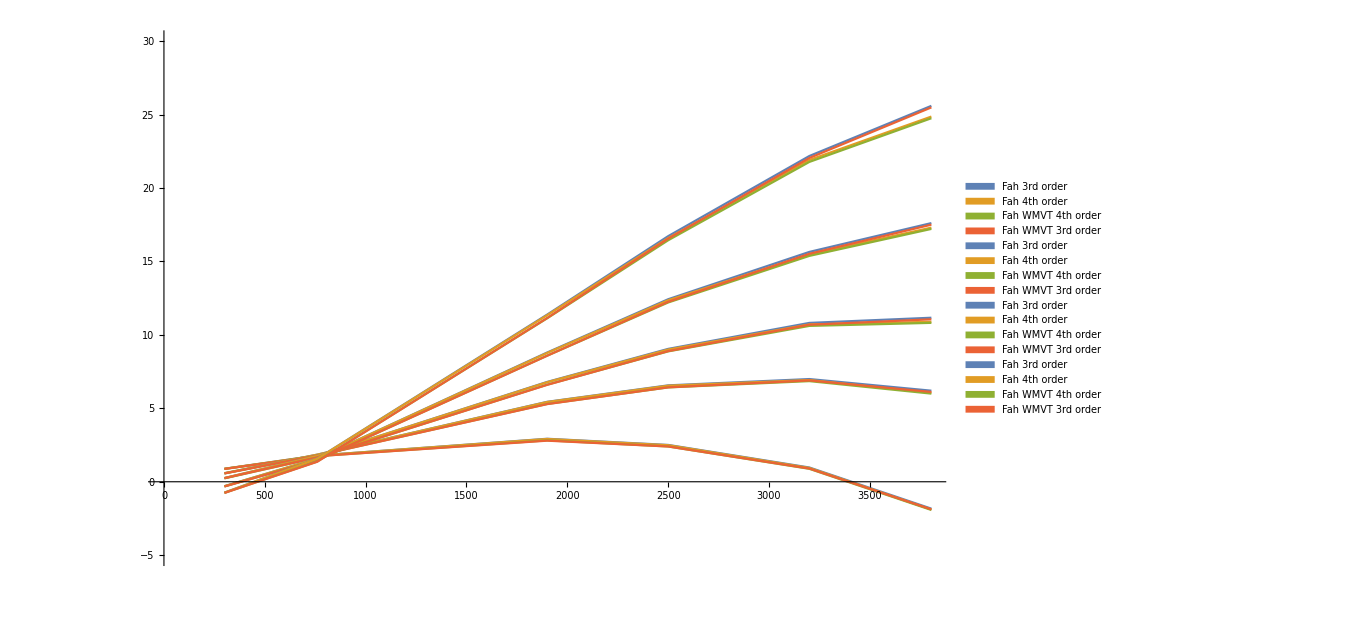

```mathematica
Show[Table[ListLinePlot[{datafahMVT3[[i]],datafahMVT4[[i]],datafahWMVT4[[i]],datafahWMVT3[[i]]},PlotRange->{{0,3800},{-5,30}},PlotLegends->SwatchLegend[{"Fah 3rd order","Fah 4th order","Fah WMVT 4th order","Fah WMVT 3rd order"}]],{i,1,5}],ImageSize->1000]
```

```mathematica
Table[Table[mvtNumWeight[dudlAllFit4[[j]][[i]],100,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,5}]//TableForm
Table[Table[mvtNumWeight[dudlAllFit3[[j]][[i]],100,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,5}]//TableForm
```

0.499954 | 0.498864 | 0.487243 | 0.480271 | 0.478089 | 0.482734
0.499895 | 0.498221 | 0.478705 | 0.469519 | 0.4693 | 0.46841
0.499824 | 0.496091 | 0.471013 | 0.464328 | 0.456043 | 0.459885
0.499886 | 0.495624 | 0.461265 | 0.449387 | 0.448115 | 0.443402
0.499883 | 0.490797 | 0.445685 | 0.437521 | 0.419754 | 0.419156

0.499935 | 0.498788 | 0.482759 | 0.475658 | 0.472774 | 0.475241
0.499876 | 0.497896 | 0.474866 | 0.46406 | 0.458784 | 0.451504
0.499959 | 0.496307 | 0.465392 | 0.454665 | 0.441288 | 0.430129
0.499835 | 0.495297 | 0.45376 | 0.436973 | 0.428327 | 0.416726
0.499816 | 0.489839 | 0.436945 | 0.41988 | 0.397751 | 0.378323